```mathematica
Remove["Global`*"]
```

### Tensor Derivative for Modified Hyperbolic Drucker Prager Root Form.

#### Part 1. Define and Verify the Vector and Operator System.

(Develped by Yuan Feng 11/20/2016 at UC Davis)

#### (1) Define the vector system

```mathematica
SetAttributes[δ,Orderless];
SetAttributes[σ,Orderless];
SetAttributes[s,Orderless];
SetAttributes[α,Orderless];
δ[i_Integer,j_Integer]:=If[i==j,1,0];
δ[i_,i_]:=3;
s[i_,i_]:= 0;
α[i_,i_]:= 0;
σ[i_,i_]:=-3 p;
```

#### (2) Define Operator Plus

```mathematica
Unprotect[Plus];
σ[i_,j_]+p δ[i_,j_]:=s[i,j]
Protect[Plus];
```

#### (3) Define Operator Multiplication.

```mathematica
Unprotect[Times];
Times[δ[i_,j_],δ[i_,j_]]:=δ[i,i] ;
Times[δ[i_,j_],δ[i_,k_]]:=δ[k,j] ;
Times[σ[i_,j_],δ[i_,j_]]:=σ[j,j];
Times[σ[i_,j_],δ[i_,k_]]:=σ[j,k];
Times[s[i_,j_],δ[i_,j_]]:=s[i,i];
Times[s[i_,j_],δ[i_,k_]]:=s[j,k];
Times[α[i_,j_],δ[i_,j_]]:=α[i,i];
Times[α[i_,j_],δ[i_,k_]]:=α[j,k];
Times[a_,δ[i_,j_]+b_]:=a δ[i,j] + a b;
Times[a_,σ[i_,j_]+b_]:=a σ[i,j] + a b;
Times[a_,s[i_,j_]+b_]:=a s[i,j] + a b;
Times[a_,α[i_,j_]+b_]:=a α[i,j] + a b;
Times[s[i_,j_] ,α[i_,j_]]:= sα;
Protect[Times];
```

#### (4) Define Operator Power.

```mathematica
Unprotect[Power];
Power[(s[i_,j_]-p α[i_,j_]),2]:=r^2;
Power[(s[i_,j_]),2]:=s^2;
Power[α[i_,j_],2]:=α^2;
Protect[Power];
```

#### (5) Define Operator D .

##### (5.1) For derivative over σ

```mathematica
Unprotect[D];
D[p,σ[i_,j_]]:=-1/3 δ[i,j];
D[s[i_,j_],σ[k_,l_]]:=δ[i,k] δ[j,l] - 1/3 δ[i,j] δ[k,l];
D[s^2,σ[i_,j_]]:=2 s[i,j]  ;
D[r,σ[i_,j_]]:=1/(3  r)(3 s[i,j]-3 p α[i,j]+sα δ[i,j]-p α^2 δ[i,j]);
D[sα,σ[i_,j_]]:=α[i,j];
D[Times[a_,b_],σ[i_,j_]]:=D[a,σ[i,j]] b + a D[b,σ[i,j] ];
D[Plus[a_,b_],σ[i_,j_]]:=D[a,σ[i,j]] +  D[b,σ[i,j] ];
D[Power[a_,n_],σ[i_,j_]]:=n Power[a,(n-1)] D[a,σ[i,j]] ;
Protect[D];
```

##### (5.2) For derivative over α

```mathematica
Unprotect[D];
D[α[i_,j_],α[k_,l_]]:=δ[i,k]δ[j,l];
D[r,σ[i_,j_]]:=(-2 p s[i,j]+2 p^2 α[i,j])/(2 √(p^2 α^2+s^2-2 p sα));
D[sα,α[i_,j_]]:=s[i,j];
D[α^2,α[i_,j_]]:=2 α[i,j];
D[Times[a_,b_],α[i_,j_]]:=(D[a,α[i,j]] )(b) + (a)( D[b,α[i,j] ]);
D[Plus[a_,b_],α[i_,j_]]:=D[a,α[i,j]] +  D[b,α[i,j] ];
D[Power[a_,n_],α[i_,j_]]:=n Power[a,(n-1)] D[a,α[i,j]] ;
Protect[D];
```

##### (5.3) For derivative over η, especially for η̄.

```mathematica
Unprotect[D];
D[η̄,η]:=0;
D[Times[a_,b_],η]:=(D[a,η] )(b) + (a)( D[b,η ]);
D[Plus[a_,b_],η]:=D[a,η] +  D[b,η ];
D[Power[a_,n_],η]:=n Power[a,(n-1)] D[a,η] ;
Protect[D];
```

#### (6) Test Cases

##### (6.1) Simple Test Case

```mathematica
Simplify[D[  √((s[o,t] - p α[o,t] ) (s[o,t] - p α[o,t] ) ),σ[i,j]]]
```

(3 s[i,j]-3 p α[i,j]+(sα-p α^2) δ[i,j])/(3 √(s^2+p (-2 sα+p α^2)))

```mathematica
Simplify[D[(3 s[i,j]-3 p α[i,j]+(sα-p α^2) δ[i,j])/(3 √(s^2+p (-2 sα+p α^2))),σ[a,b]]]
```

1/(9 (s^2+p (-2 sα+p α^2))^(3/2))((3 s[a,b]-3 p α[a,b]+(sα-p α^2) δ[a,b]) (-3 s[i,j]+3 p α[i,j]+(-sα+p α^2) δ[i,j])+(s^2+p (-2 sα+p α^2)) (3 α[i,j] δ[a,b]+9 δ[a,i] δ[b,j]+(3 α[a,b]+(-3+α^2) δ[a,b]) δ[i,j]))

##### (6.2) Advanced Test Case (Verified to existing tensor derivatives to Lecture notes)

```mathematica
testF=(( s[i,j]-p α[i,j])(s[i,j]-p α[i,j]))^0.5-√(2/3)η p  ;
```

(6.2.1) Normal to yield surface. Correct!

```mathematica
testN=D[testF,σ[k,l]];
```

```mathematica
Simplify[testN]
```

(1. s[k,l]-1. p α[k,l]+(0.333333 sα-0.333333 p α^2+0.272166 (s^2-2 p sα+p^2 α^2)^0.5 η) δ[k,l])/((s^2-2 p sα+p^2 α^2)^0.5)

(6.2.2) Normal to yield surface for α. Correct!

```mathematica
testN4α=D[testF,α[k,l]];
```

```mathematica
Simplify[testN4α]
```

(p (-1. s[k,l]+1. p α[k,l]))/((s^2-2 p sα+p^2 α^2)^0.5)

(6.2.3) Normal to yield surface for η. Correct!

```mathematica
testN4η=D[testF,η]
```

0.-√(2/3) p

(6.2.4) Associated plastic flow and its derivative to σ. Correct!

```mathematica
testM4σ=D[testN,σ[i,j]]
```

0.5 (-(0.5 (2 s[i,j]-2/3 p α^2 δ[i,j]-2 (p α[i,j]-1/3 sα δ[i,j])) (2 s[k,l]-2/3 p α^2 δ[k,l]-2 (p α[k,l]-1/3 sα δ[k,l])))/((s^2-2 p sα+p^2 α^2)^1.5)+(2/9 α^2 δ[i,j] δ[k,l]-2 (-1/3 α[k,l] δ[i,j]-1/3 α[i,j] δ[k,l])+2 (δ[i,k] δ[j,l]-1/3 δ[i,j] δ[k,l]))/((s^2-2 p sα+p^2 α^2)^0.5))

```mathematica
Simplify[testM4σ];
```

(6.2.5) Associated plastic flow and its derivative to α. Correct!

```mathematica
testM4α = D[testN,α[i,j]]
```

0.5 (-(0.5 (-2 p s[i,j]+2 p^2 α[i,j]) (2 s[k,l]-2/3 p α^2 δ[k,l]-2 (p α[k,l]-1/3 sα δ[k,l])))/((s^2-2 p sα+p^2 α^2)^1.5)+(-4/3 p α[i,j] δ[k,l]-2 (p δ[i,k] δ[j,l]-1/3 s[i,j] δ[k,l]))/((s^2-2 p sα+p^2 α^2)^0.5))

(6.2.6) Associated plastic flow and its derivative to η. Correct!

```mathematica
testM4η=D[testN,η]
```

0.+1/3 √(2/3) δ[k,l]

#### Part 2. Tensor Derivative for the Model

#### (7) Real Model: Modified Hyperbolic Yield Surface

##### (7.1) Yield Surface

```mathematica
Φ=-ξ+(1/2(s[i,j]-p α[i,j])(s[i,j]-p α[i,j])+η^2  roundedLength^2)^0.5-η  p;
```

```mathematica
ΦSimplified = Rationalize[FullSimplify[Φ,η>0,ExcludedForms->Power[_Rational]]]
```

-p η+√(s^2/2-p (sα-(p α^2)/2)+roundedLength^2 η^2)-ξ

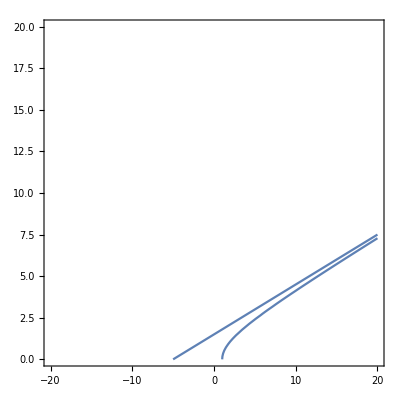

```mathematica
centerP = 5;range=20;Slope = 0.3; distP =6;
fig1 = ContourPlot[-centerP +√(q^2/Slope^2+distP^2)-p==0,{p,-range,range},{q,0,range}];
figRef=ContourPlot[yy == Slope *(xx+centerP), {xx,-centerP,range},{yy,0,range}];
Show[fig1,figRef]
```

(7.1.1) Normal to the yield surface for σ. Namely, (∂ Φ)/(∂σ_ij)

```mathematica
n=D[Φ,σ[k,l]];
```

```mathematica
nSimplified=Rationalize[FullSimplify[n,η>0,ExcludedForms->Power[_Rational]]]
```

1/3 η δ[k,l]+(1/2 s[k,l]-1/2 p α[k,l]+(sα/6-(p α^2)/6) δ[k,l])/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))

(7.1.2) Normal to the yield surfoce for α. Namely, (∂Φ)/(∂α_ij)

```mathematica
phi4alpha=D[Φ,α[k,l]];
```

```mathematica
phi4alphaSimplified=Rationalize[FullSimplify[phi4alpha,η>0,ExcludedForms->Power[_Rational]]]
```

(p (-1/2 s[k,l]+1/2 p α[k,l]))/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))

(7.1.3) Normal to the yield surface for η. Namely, (∂Φ)/(∂η)

```mathematica
phi4eta=D[Φ,η];
```

```mathematica
phi4etaSimplified=Rationalize[FullSimplify[phi4eta,η>0,ExcludedForms->Power[_Rational]]]
```

-p+(roundedLength^2 η)/(√(s^2/2-p (sα-(p α^2)/2)+roundedLength^2 η^2))

(7.1.4) n for α. Namely, (∂n)/(∂α_ij)

```mathematica
n4α=D[Φ,α[k,l]]
```

(0.5 (-1/2 p s[k,l]-p (-1/2 p α[k,l]+(1/2 s[i,j]-1/2 p α[i,j]) δ[i,k] δ[j,l])))/((roundedLength^2 η^2+s[i,j] (1/2 s[i,j]-1/2 p α[i,j])-p α[i,j] (1/2 s[i,j]-1/2 p α[i,j]))^0.5)

```mathematica
n4αSimplified=Rationalize[FullSimplify[n4α,η>0,ExcludedForms-> Power[_Rational]]]
```

(p (-1/2 s[k,l]+1/2 p α[k,l]))/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))

(7.1.5) n for η. Namely, (∂n)/(∂η)

```mathematica
n4η=D[Φ,η];
```

```mathematica
n4ηSimplified = Rationalize[FullSimplify[n4η,η>0,ExcludedForms->Power[_Rational]]]
```

-p+(roundedLength^2 η)/(√(s^2/2-p (sα-(p α^2)/2)+roundedLength^2 η^2))

##### (7.2) Plastic Flow Potential

(Notes: assume m=n in the beginning, modified the non-associative plastic flow later.)

```mathematica
ψ =-ξ+(1/2(s[i,j]-p α[i,j])(s[i,j]-p α[i,j])+η^2  roundedLength^2)^0.5-η  p;
```

```mathematica
centerP2 = 5;range2=20;Slop2 = 0.1;
fig2 = ContourPlot[-centerP2 +√(q^2/Slop2^2+distP^2)-p==0,{p,-range2,range2},{q,0,range2}];
(*Show[fig1,fig2]*)
```

(7.2.1) Plastic flow direction, normal to the plastic potential. Namely, (∂ψ)/(∂σ_ij).

```mathematica
m=D[ψ,σ[k,l]]
```

1/3 η δ[k,l]+(0.5 (1/3 α[i,j] (1/2 s[i,j]-1/2 p α[i,j]) δ[k,l]+(1/2 s[i,j]-1/2 p α[i,j]) (δ[i,k] δ[j,l]-1/3 δ[i,j] δ[k,l])+s[i,j] (1/6 α[i,j] δ[k,l]+1/2 (δ[i,k] δ[j,l]-1/3 δ[i,j] δ[k,l]))-p α[i,j] (1/6 α[i,j] δ[k,l]+1/2 (δ[i,k] δ[j,l]-1/3 δ[i,j] δ[k,l]))))/(roundedLength^2 η^2+s[i,j] (1/2 s[i,j]-1/2 p α[i,j])-p α[i,j] (1/2 s[i,j]-1/2 p α[i,j]))^0.5

```mathematica
mSimplified = Rationalize[FullSimplify[m,η̄>0,ExcludedForms->{Power[_Rational]}]]
```

1/3 η δ[k,l]+(1/2 s[k,l]-1/2 p α[k,l]+(sα/6-(p α^2)/6) δ[k,l])/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))

(Notes: the non-associative plastic flow should use the deviatoric part of the normal to the yield surface only
                        and then added the volumetric part).

```mathematica
mSimplified_dev =(1/2 s[k,l]-1/2 p α[k,l])/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))
```

(1/2 s[k,l]-1/2 p α[k,l])/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))

(So the non-associative plastic flow rule is as follows)

```mathematica
m = (1/2 s[k,l]-1/2 p α[k,l])/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))+ 1/3 η̄ δ[k,l]
```

(1/2 s[k,l]-1/2 p α[k,l])/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))+1/3 η̄ δ[k,l]

```mathematica
mSimplified = m
```

(1/2 s[k,l]-1/2 p α[k,l])/(√(s^2/2-p sα+(p^2 α^2)/2+roundedLength^2 η^2))+1/3 η̄ δ[k,l]

(7.2.2) Useful derivative with plastic flow m_ij . For the stress, (∂m_kl)/(∂σ_ij).

```mathematica
m4σ=D[m,σ[i,j]];
```

```mathematica
m4σSimplified = Rationalize[FullSimplify[m4σ,η̄>0,ExcludedForms->{Power[_Rational]}]]
```

((1/2 s[k,l]-1/2 p α[k,l]) (-s[i,j]+p α[i,j]-(sα/3-(p α^2)/3) δ[i,j]))/(2 (-p sα+1/2 (s^2+p^2 α^2)+roundedLength^2 η^2)^(3/2))+(1/2 δ[i,k] δ[j,l]+δ[i,j] (1/6 α[k,l]-1/6 δ[k,l]))/(√(-p sα+1/2 (s^2+p^2 α^2)+roundedLength^2 η^2))

(7.2.3) Useful derivative with plastic flow m_ij . For the backstress, (∂m_kl)/(∂α_ij).

```mathematica
m4α=D[m,α[i,j]];
```

```mathematica
m4αSimplified=Rationalize[FullSimplify[m4α,η̄>0,ExcludedForms->{Power[_Rational]}]]
```

1/2 (-(p (-s[i,j]+p α[i,j]) (1/2 s[k,l]-1/2 p α[k,l]))/((-p sα+1/2 (s^2+p^2 α^2)+roundedLength^2 η^2)^(3/2))-(p δ[i,k] δ[j,l])/(√(-p sα+1/2 (s^2+p^2 α^2)+roundedLength^2 η^2)))

(7.2.4) Useful derivative with plastic flow m_ij  . For the slope, (∂m_kl)/(∂ η).

```mathematica
m4η=D[m,η];
```

```mathematica
m4ηSimplified =Rationalize[FullSimplify[m4η,η̄>0,ExcludedForms->{Power[_Rational]}]]
```

-(roundedLength^2 η (1/2 s[k,l]-1/2 p α[k,l]))/((-p sα+1/2 (s^2+p^2 α^2)+roundedLength^2 η^2)^(3/2))

#### (8) Output in C Format

```mathematica
CForm[FullSimplify[Φ]]
```

-(p*η) + 0.7071067811865476*Power(Power(s,2) - 2*p*sα + 
      Power(p,2)*Power(α,2) + 2*Power(roundedLength,2)*Power(η,2),0.5) - ξ

```mathematica
file=OpenWrite["MHDruckerPrager_TensorDerivative_Simplify_nonassociative.cpp"];
WriteString[file,"f=\n"]
WriteString[file,CForm[ΦSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"n=\n"]
WriteString[file,CForm[nSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"phi4alpha=\n"]
WriteString[file,CForm[phi4alphaSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"phi4eta=\n"]
WriteString[file,CForm[phi4etaSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"dn_over_dalpha=\n"]
WriteString[file,CForm[n4αSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"dn_dEta=\n"]
WriteString[file,CForm[n4ηSimplified ]]
WriteString[file,";\n\n\n\n"]


WriteString[file,"Q=\n"]
WriteString[file,CForm[ψ]]
WriteString[file,";\n\n"]
WriteString[file,"m=\n"]
WriteString[file,CForm[mSimplified ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dsigma=\n"]
WriteString[file,CForm[m4σSimplified ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dalpha=\n"]
WriteString[file,CForm[m4αSimplified ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dEta=\n"]
WriteString[file,CForm[m4ηSimplified ]]
WriteString[file,";\n\n\n"]
Close[file];
```

##### (8.2) Not Simplify.

```mathematica
file=OpenWrite["MHDruckerPrager_TensorDerivative_Full_nonassociative.cpp"];
WriteString[file,"f=\n"]
WriteString[file,CForm[Φ]]
WriteString[file,";\n\n"]
WriteString[file,"n=\n"]
WriteString[file,CForm[n]]
WriteString[file,";\n\n"]
WriteString[file,"phi4alpha=\n"]
WriteString[file,CForm[phi4alpha]]
WriteString[file,";\n\n"]
WriteString[file,"phi4eta=\n"]
WriteString[file,CForm[phi4eta]]
WriteString[file,";\n\n"]
WriteString[file,"df_over_dalpha=\n"]
WriteString[file,CForm[n4α ]]
WriteString[file,";\n\n"]
WriteString[file,"df_dEta=\n"]
WriteString[file,CForm[n4η ]]
WriteString[file,";\n\n\n\n"]

WriteString[file,"Q=\n"]
WriteString[file,CForm[ψ]]
WriteString[file,";\n\n"]
WriteString[file,"m=\n"]
WriteString[file,CForm[m ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dsigma=\n"]
WriteString[file,CForm[m4σ ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dalpha=\n"]
WriteString[file,CForm[m4α ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dEta=\n"]
WriteString[file,CForm[m4η ]]
WriteString[file,";\n\n\n"]
Close[file];
```

#### (9) Output in latex format

```mathematica
file=OpenWrite["MHDruckerPrager_TensorDerivative_Simplify_nonassociative.tex"];
WriteString[file,"f=\n"]
WriteString[file,TeXForm[ΦSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"n=\n"]
WriteString[file,TeXForm[nSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"phi4alpha=\n"]
WriteString[file,TeXForm[phi4alphaSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"phi4eta=\n"]
WriteString[file,TeXForm[phi4etaSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"dn_over_dalpha=\n"]
WriteString[file,TeXForm[n4αSimplified]]
WriteString[file,";\n\n"]
WriteString[file,"dn_dEta=\n"]
WriteString[file,TeXForm[n4ηSimplified ]]
WriteString[file,";\n\n\n\n"]


WriteString[file,"Q=\n"]
WriteString[file,TeXForm[ψ]]
WriteString[file,";\n\n"]
WriteString[file,"m=\n"]
WriteString[file,TeXForm[mSimplified ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dsigma=\n"]
WriteString[file,TeXForm[m4σSimplified ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dalpha=\n"]
WriteString[file,TeXForm[m4αSimplified ]]
WriteString[file,";\n\n"]
WriteString[file,"dm_over_dEta=\n"]
WriteString[file,TeXForm[m4ηSimplified ]]
WriteString[file,";\n\n\n"]
Close[file];
```